```mathematica
a
```

a

```mathematica
usbcs={"adcirc_flow","adcirc_stage","rdhm_flow"};
dsbcs={"adcirc_stage","stage_0","noriver_adcirc_stage"};
sites={"greenville","rock_springs","grimesland"};
```

```mathematica
eventname="irene";
r=StringJoin["D:\\Dropbox\\",eventname];
```

# Greenville

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-432, na], Max[12801, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

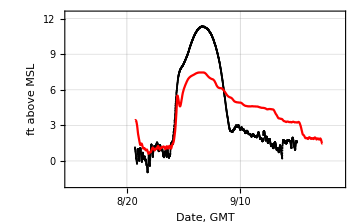
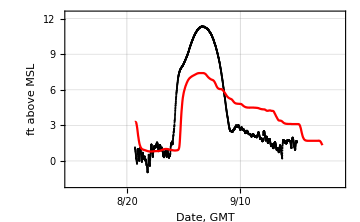
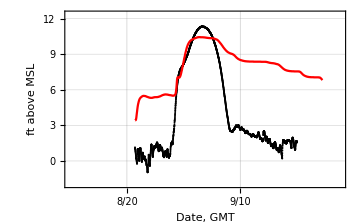
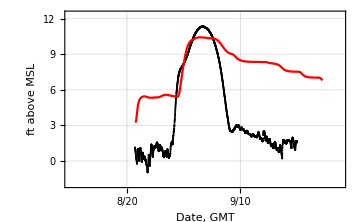
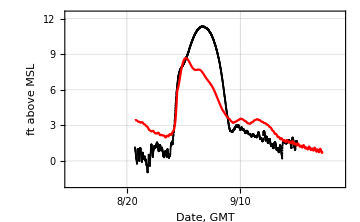
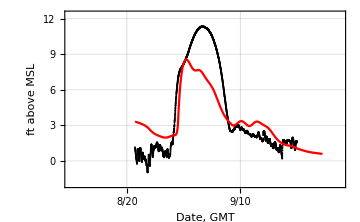
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

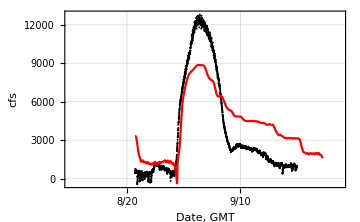
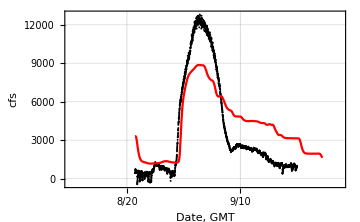
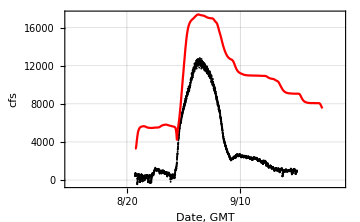
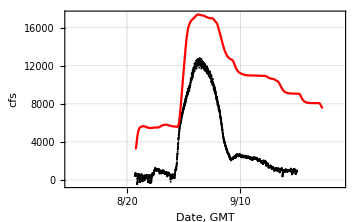
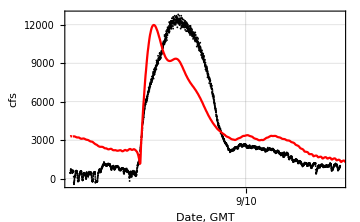
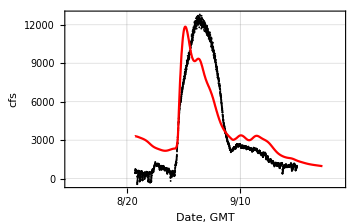
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="greenville";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
flowplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"flow"];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".eps"],flowplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".wmf"],flowplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
flowplots//MatrixForm
```

# Rock Springs

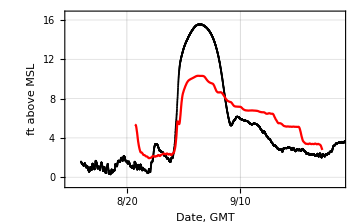
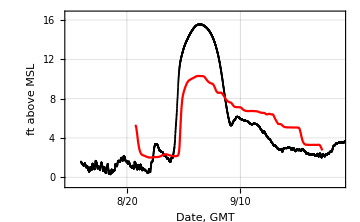
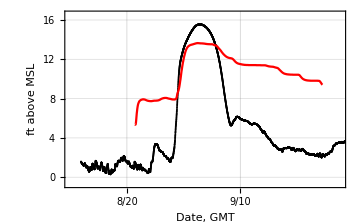
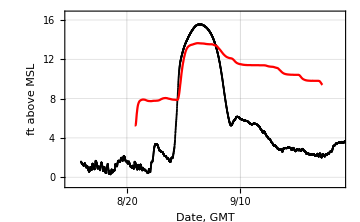
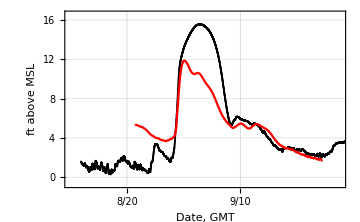
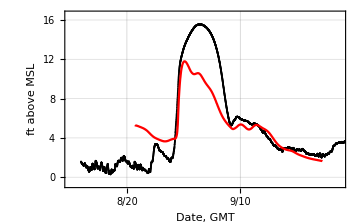
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="rock_springs";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

# Grimesland

(hecplot[irene,adcirc_flow,adcirc_stage,grimesland,stage] | hecplot[irene,adcirc_flow,stage_0,grimesland,stage] | 0 | 0
hecplot[irene,adcirc_stage,adcirc_stage,grimesland,stage] | hecplot[irene,adcirc_stage,stage_0,grimesland,stage] | 0 | 0
hecplot[irene,rdhm_flow,adcirc_stage,grimesland,stage] | hecplot[irene,rdhm_flow,stage_0,grimesland,stage] | 0 | 0
0 | 0 | 0 | 0)

Transpose::nmtx: The first two levels of {{3.51891×10^9, 3.51891×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, « 16 », 3.51894×10^9, 3.51894×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, « 9837 »}, {« 1 »}} cannot be transposed.

ToExpression::notstrbox: Transpose[{{3.51891×10^9, 3.51891×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, « 17 », 3.51894×10^9, 3.51894×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, « 9837 »}, {na, na, « 48 », « 28750 »}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Transpose::nmtx: The first two levels of {{3.52279×10^9, 3.52279×10^9, 3.52279×10^9, 3.5228×10^9, 3.5228×10^9, 3.52281×10^9, 3.52281×10^9, 3.52281×10^9, 3.52282×10^9, 3.52282×10^9, 3.52282×10^9, 3.52283×10^9, 3.52283×10^9, 3.52283×10^9, 3.52284×10^9, 3.52284×10^9, 3.52285×10^9, 3.52285×10^9, 3.52285×10^9, 3.52286×10^9, 3.52286×10^9, 3.52286×10^9, 3.52287×10^9, « 5 », 3.52289×10^9, 3.52289×10^9, 3.5229×10^9, 3.5229×10^9, 3.5229×10^9, 3.52291×10^9, 3.52291×10^9, 3.52291×10^9, 3.52292×10^9, 3.52292×10^9, 3.52292×10^9, 3.52293×10^9, 3.52293×10^9, 3.52293×10^9, 3.52294×10^9, 3.52294×10^9, 3.52295×10^9, 3.52295×10^9, 3.52295×10^9, 3.52296×10^9, 3.52296×10^9, 3.52296×10^9, « 784 »}, {« 1 »}} cannot be transposed.

ToExpression::notstrbox: Transpose[{{3.52279×10^9, 3.52279×10^9, 3.52279×10^9, 3.5228×10^9, 3.5228×10^9, 3.52281×10^9, 3.52281×10^9, 3.52281×10^9, 3.52282×10^9, 3.52282×10^9, 3.52282×10^9, 3.52283×10^9, 3.52283×10^9, 3.52283×10^9, 3.52284×10^9, 3.52284×10^9, 3.52285×10^9, 3.52285×10^9, 3.52285×10^9, 3.52286×10^9, 3.52286×10^9, 3.52286×10^9, 3.52287×10^9, « 6 », 3.52289×10^9, 3.5229×10^9, 3.5229×10^9, 3.5229×10^9, 3.52291×10^9, 3.52291×10^9, 3.52291×10^9, 3.52292×10^9, 3.52292×10^9, 3.52292×10^9, 3.52293×10^9, 3.52293×10^9, 3.52293×10^9, 3.52294×10^9, 3.52294×10^9, 3.52295×10^9, 3.52295×10^9, 3.52295×10^9, 3.52296×10^9, 3.52296×10^9, 3.52296×10^9, « 784 »}, {« 1 »}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[obflowscatter].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::lpn: obflowscatter is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[obflowscatter, Joined → False, PlotRange → {{3521923200, 3526243200}, {-30434.74`, 14012.16`}}, Frame → True, FrameTicks → {{Automatic, None}, {{{3522225600, .

Transpose::nmtx: The first two levels of {{3.51891×10^9, 3.51891×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, « 16 », 3.51894×10^9, 3.51894×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, « 9837 »}, {« 1 »}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ToExpression::notstrbox: Transpose[{{3.51891×10^9, 3.51891×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51892×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, 3.51893×10^9, « 17 », 3.51894×10^9, 3.51894×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51895×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, 3.51896×10^9, « 9837 »}, {na, na, « 48 », « 28750 »}}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[obflowscatter, Joined → False, PlotRange → {{3521923200, 3526243200}, {172.22000000000003`, 9820.84`}}, Frame → True, FrameTicks → {{Automatic, None}, {{{3522225600, .

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

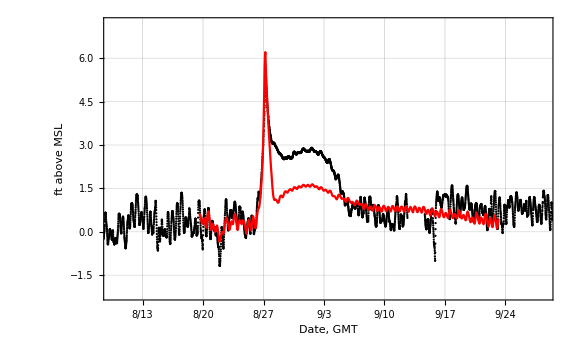
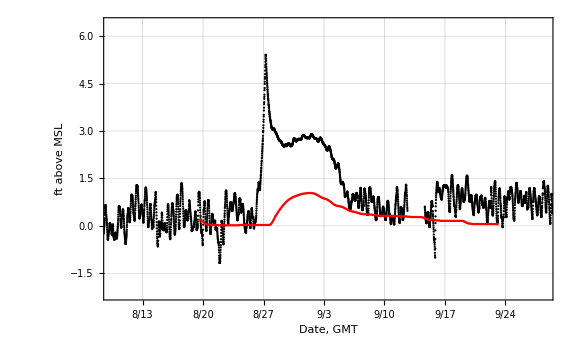
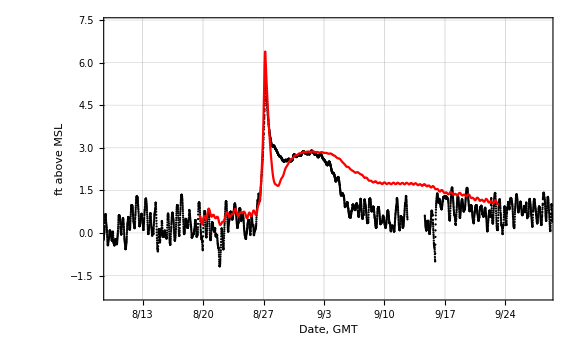
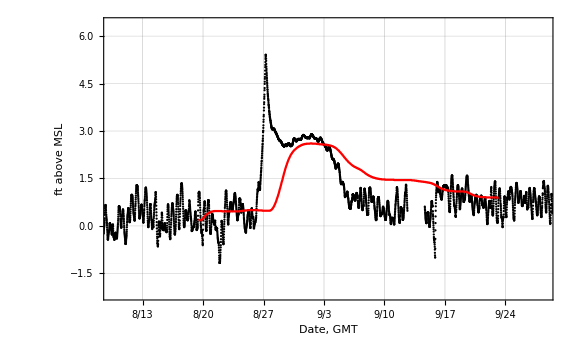
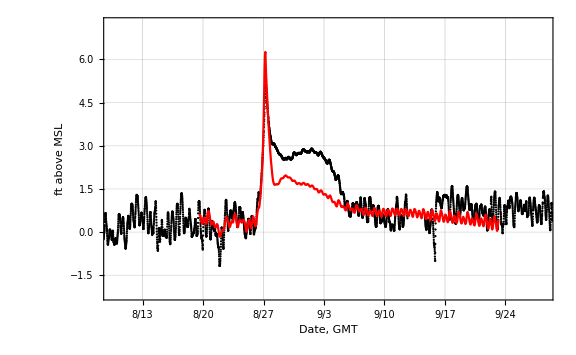
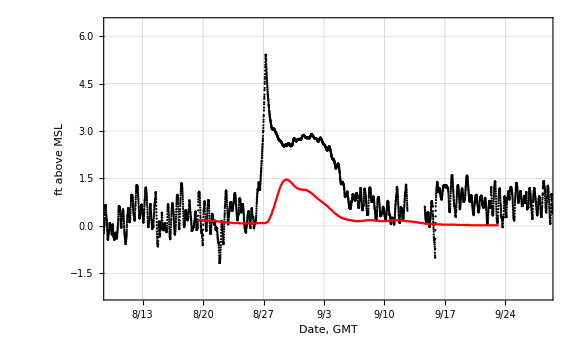
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

(Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{-30434.7,14012.2}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_flow / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{-30434.7,14012.2}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_flow / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{172.22,9820.84}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_flow / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{172.22,9820.84}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_flow / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | 0 | 0
Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{-28636.6,18333.3}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_stage / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{-28636.6,18333.3}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_stage / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{2273.6,18253.6}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_stage / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{2273.6,18253.6}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,adcirc_stage / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | 0 | 0
Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{-30021.6,15019.7}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,rdhm_flow / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{-30021.6,15019.7}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,rdhm_flow / adcirc_stage}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | Show[ListPlot[obflowscatter,Joined→False,PlotRange→{{3521923200,3526243200},{-23.56,12081.}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,rdhm_flow / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-],ListPlot[hecflowscatter,Joined→True,PlotRange→{{3521923200,3526243200},{-23.56,12081.}},Frame→True,FrameTicks→{{Automatic,None},{{{3522225600,8/13},{3522830400,8/20},{3523435200,8/27},{3524040000,9/3},{3524644800,9/10},{3525249600,9/17},{3525854400,9/24},{3526459200,10/1}},None}},FrameLabel→{{cfs,None},{Date, GMT,rdhm_flow / stage_0}},GridLines→{{3522225600,3522830400,3523435200,3524040000,3524644800,3525249600,3525854400,3526459200},Automatic},BaseStyle→{FontSize→14,FontFamily→Times New Roman},ImageSize→Large,PlotStyle→-Graphics-]] | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="grimesland";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm








sitename="grimesland";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage",True,Red];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
flowplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"flow",True,Red];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".eps"],flowplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".wmf"],flowplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
flowplots//MatrixForm
```

## Pamlico at Washington

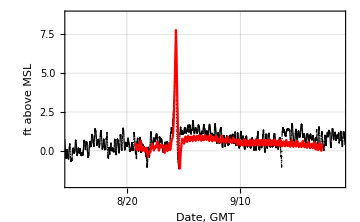
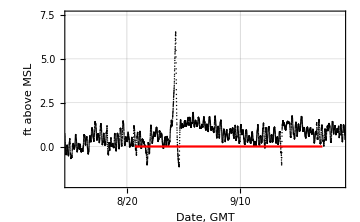
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="washington";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

## Tar at Tarboro

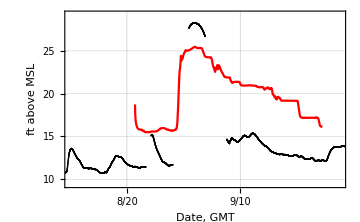
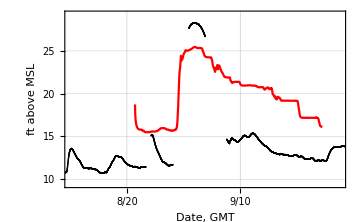
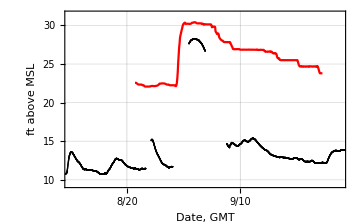
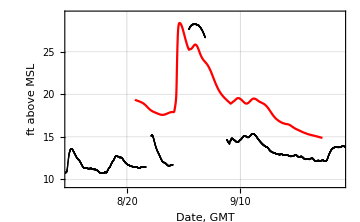
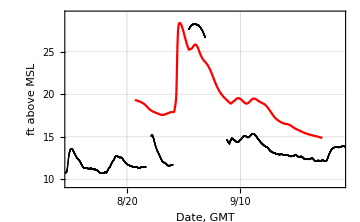
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="tarboro";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```